```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Directory[]
```

/Users/npadmana/myWork/np_sandbox/CLASS

```mathematica
ff = Import["output/test_z1_pk.dat","Table"]//DeleteCases[#, {"#",___}] & ;
```

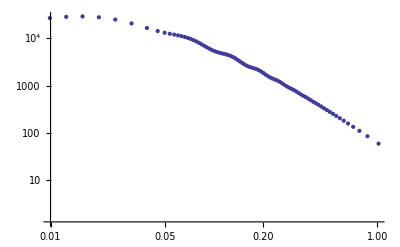

```mathematica
ListLogLogPlot[ff, PlotRange->{{0.01, 1}, All}]
```

```mathematica
gg = Import["output/test_z1_tk.dat", "Table"]//DeleteCases[#, {"#", ___}] & // Part[#, All, {1,8}] & ;
```

```mathematica
gg1 = MapThread[{#1, #2/-#1} &, Transpose[gg]];
```

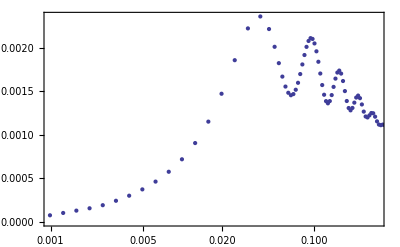

```mathematica
ListLogLinearPlot[gg1, PlotRange->{{0.001, 0.3}, All}, Frame->True]
```

```mathematica
gg1//TableForm
```

1.97552×10^-7 | 1.71399×10^-15
2.48704×10^-7 | 3.41986×10^-15
3.13099×10^-7 | 6.82372×10^-15
3.94169×10^-7 | 1.36148×10^-14
4.96229×10^-7 | 2.71651×10^-14
6.24715×10^-7 | 5.42011×10^-14
7.8647×10^-7 | 1.08148×10^-13
9.90107×10^-7 | 2.15782×10^-13
1.24647×10^-6 | 4.3053×10^-13
1.56921×10^-6 | 8.59043×10^-13
1.97552×10^-6 | 1.71398×10^-12
2.48704×10^-6 | 3.41963×10^-12
3.13099×10^-6 | 6.82291×10^-12
3.94169×10^-6 | 1.36146×10^-11
4.96229×10^-6 | 2.71644×10^-11
6.24715×10^-6 | 5.41989×10^-11
7.8647×10^-6 | 1.08138×10^-10
9.90107×10^-6 | 2.15752×10^-10
0.0000124647 | 4.30446×10^-10
0.0000156921 | 8.58742×10^-10
0.0000197552 | 1.71306×10^-9
0.0000248704 | 3.41688×10^-9
0.0000313099 | 6.81404×10^-9
0.0000394169 | 1.35846×10^-8
0.0000496229 | 2.70695×10^-8
0.0000624715 | 5.38992×10^-8
0.000078647 | 1.07192×10^-7
0.0000990107 | 2.12771×10^-7
0.000124647 | 4.21076×10^-7
0.000156921 | 8.29383×10^-7
0.000197552 | 1.62157×10^-6
0.000248704 | 3.13412×10^-6
0.000313099 | 5.95133×10^-6
0.000394169 | 0.0000110036
0.000496229 | 0.0000195693
0.000624715 | 0.0000329857
0.00078647 | 0.0000519687
0.000990107 | 0.0000759565
0.00124647 | 0.00010292
0.00156921 | 0.000129688
0.00197552 | 0.000156646
0.00248704 | 0.00019214
0.00313099 | 0.000243024
0.00394169 | 0.000301381
0.00496229 | 0.000373893
0.00624715 | 0.000463653
0.0078647 | 0.000576734
0.00990107 | 0.000720241
0.0124647 | 0.000906932
0.0156921 | 0.00115341
0.0197552 | 0.00147416
0.0248702 | 0.00186015
0.0312932 | 0.00222585
0.038861 | 0.00236322
0.0452391 | 0.00221844
0.0498651 | 0.00201425
0.0536803 | 0.00182616
0.0570869 | 0.00167145
0.0602641 | 0.00155689
0.063307 | 0.00148535
0.0662725 | 0.00145717
0.0691979 | 0.00147028
0.0721095 | 0.0015202
0.0750271 | 0.00160002
0.077966 | 0.00170067
0.0809388 | 0.00181123
0.083956 | 0.00191962
0.0870268 | 0.00201351
0.0901596 | 0.00208134
0.0933617 | 0.00211377
0.0966404 | 0.0021048
0.100002 | 0.00205298
0.103453 | 0.00196229
0.107 | 0.0018421
0.110649 | 0.00170682
0.114405 | 0.00157417
0.118274 | 0.00146278
0.122263 | 0.00138912
0.126376 | 0.001364
0.130621 | 0.00138982
0.135002 | 0.0014587
0.139526 | 0.00155306
0.144197 | 0.00164827
0.149023 | 0.00171792
0.154008 | 0.00174059
0.15916 | 0.00170621
0.164483 | 0.00162051
0.169983 | 0.00150478
0.175668 | 0.00139062
0.181542 | 0.00130989
0.187613 | 0.00128318
0.193887 | 0.00131092
0.200371 | 0.0013718
0.207072 | 0.00143052
0.213997 | 0.00145312
0.221154 | 0.00142322
0.228552 | 0.00135105
0.2362 | 0.00126869
0.244107 | 0.0012125
0.252283 | 0.00120158
0.260742 | 0.00122564
0.269495 | 0.0012522
0.278556 | 0.00124962
0.287941 | 0.00121048
0.297669 | 0.00115659
0.307759 | 0.00111957
0.318234 | 0.0011126
0.329121 | 0.00111933
0.340449 | 0.00111222
0.352253 | 0.00108228
0.364574 | 0.00104743
0.377459 | 0.00102822
0.390966 | 0.0010215
0.405162 | 0.00100772
0.42013 | 0.000981684
0.43597 | 0.000958271
0.45281 | 0.00094383
0.470808 | 0.000926321
0.49017 | 0.000902765
0.51117 | 0.000882885
0.534176 | 0.000863121
0.559707 | 0.000839616
0.588518 | 0.000817159
0.62176 | 0.000791762
0.6613 | 0.000764743
0.710383 | 0.000733926
0.775156 | 0.000697895
0.868261 | 0.000653431
1.0155 | 0.000596573